```mathematica
(* https://www.reddit.com/r/math/comments/6hg9xf/probability_puzzle_apartment_leasing/ *)
```

```mathematica
IntegerPartitions[12,3]
```

{{12},{11,1},{10,2},{10,1,1},{9,3},{9,2,1},{8,4},{8,3,1},{8,2,2},{7,5},{7,4,1},{7,3,2},{6,6},{6,5,1},{6,4,2},{6,3,3},{5,5,2},{5,4,3},{4,4,4}}

```mathematica
%//Length
```

19

```mathematica
1-(6/7)^12
```

11664504865/13841287201

```mathematica
%//N
```

0.842733

```mathematica
parts=(#-{1,1,1})&/@IntegerPartitions[15,{3}]
Total[(1-(4/7)^#)&/@#]/3&/@parts
N[%]
Sort[%]
```

{{12,0,0},{11,1,0},{10,2,0},{10,1,1},{9,3,0},{9,2,1},{8,4,0},{8,3,1},{8,2,2},{7,5,0},{7,4,1},{7,3,2},{6,6,0},{6,5,1},{6,4,2},{6,3,3},{5,5,2},{5,4,3},{4,4,4}}

{4608169995/13841287201,940186062/1977326743,157221702/282475249,174516105/282475249,24305178/40353607,28187595/40353607,3616470/5764801,4286349/5764801,4488033/5764801,526842/823543,631947/823543,677223/823543,75702/117649,91485/117649,99297/117649,101649/117649,14295/16807,14823/16807,2145/2401}

{0.332929,0.475483,0.556586,0.61781,0.602305,0.698515,0.627336,0.743538,0.778523,0.639726,0.767352,0.822329,0.643456,0.77761,0.844011,0.864002,0.850538,0.881954,0.893378}

{0.332929,0.475483,0.556586,0.602305,0.61781,0.627336,0.639726,0.643456,0.698515,0.743538,0.767352,0.77761,0.778523,0.822329,0.844011,0.850538,0.864002,0.881954,0.893378}

```mathematica
%114-%92
```

{-0.509803,-0.367249,-0.286147,-0.224922,-0.240428,-0.144218,-0.215396,-0.0991946,-0.0642092,-0.203007,-0.0753811,-0.020404,-0.199276,-0.065123,0.00127791,0.0212696,0.0078058,0.0392213,0.0506451}

```mathematica
?Histogram
```

Histogram[{x_1,x_2,…}] plots a histogram of the values x_i.
Histogram[{x_1,x_2,…},bspec] plots a histogram with bin width specification bspec.
Histogram[{x_1,x_2,…},bspec,hspec] plots a histogram with bin heights computed according to the specification hspec.
Histogram[{data_1,data_2,…},…] plots histograms for multiple datasets data_i.

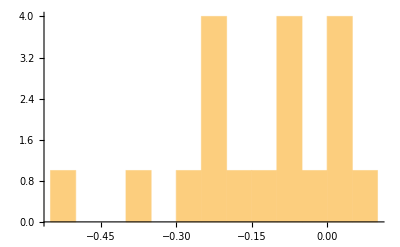

```mathematica
Histogram[%114-%92,10]
```

```mathematica
1-.3730
```

0.627

```mathematica
((1-(4/7)^6)+(1-(4/7)^4)+(1-(4/7)^2))/3
```

99297/117649

```mathematica
%//N
```

0.844011

```mathematica
Total[(1-(4/7)^#)&/@#]/3&/@parts
```

{4608169995/13841287201,940186062/1977326743,157221702/282475249,174516105/282475249,24305178/40353607,28187595/40353607,3616470/5764801,4286349/5764801,4488033/5764801,526842/823543,631947/823543,677223/823543,75702/117649,91485/117649,99297/117649,101649/117649,14295/16807,14823/16807,2145/2401}